### Mathematica Hw I1

Claus Ernst/Huanjing Wang		Math/Cs 371 Spring 2016
Due: Wednesday, February 10 before class.  
This assignment must be turned in electronically AND as a hard copy.  The electronic copy must be submitted through blackboard prior to your class.

#### General Requirements - read before you start working

Form groups of two. Each member of the group must understand and be able to explain (in detail) all of the code turned in. We allow you to work in groups so that you have someone with whom you can talk about your work in detail. This is not meant for group members to only do half of the work. 

Each group turns in one (stapled) printout at the beginning of class and submits an electronic copy (one file) prior to class.

Your electronic and hard copy must include: 
a) The names of both group members on the print out (printed from the file, not added by hand). The name of both group members must be included in the name of the electronic file. For example if we (Claus and Huanjing) are a team then the file name should be ErnstWang371Hw2.nb. This will help to identify whose file we are looking at and it will also avoid having several different files with the same name.
b) A solution to each problem, which includes the code, as well as a couple of executions of your code which demonstrate that the code is (most likely) correct. Select different types of input for your example runs, to show that different parts of your code work correctly.   
Your solutions must be well-documented Mathematica code, that is, you must use comments, meaningful variable names, proper indentations, hide local variables (if any are needed), etc.  The comments in the code should be such that taken by themselves they describe the algorithm you used.

Note: Throughout this assignment, the lists of arguments for functions are given to clarify the order and meaning of the arguments; they do not follow Mathematica syntax. However, your solutions must follow the given order/structure of arguments as specified by the assignment. If you do deviate from this our test programs will not run.

### Problem 1: How old?

Write a function uHowOld [year, month, day] which is given the date of birth of a person as parameters and which returns the age of the person (an integer). For example,  uHowOld[1994, 1, 18] returns 22  and uHowOld[ 1994, 2, 3] returns 21 - if executed prior to February 3rd, 2016.  Mathematica has a function called Date which returns the current date in an array.

### Problem 2: Reverse an integer

Write a function reverseInteger [x] which takes an integer value and returns the number with its digits reversed. For example, given the number 76543, the function should return 34567. 

Warning: Do not use existing Mathematica Reverse function. Use a loop inside the function reverseInteger [x].

### Problem 3: Locker doors

There are n lockers in a hallway, number sequentially from 1 to n. Initially all the locker doors are closed. You make n passes by the lockers, each time starting with locker #1. On the ith pass, i = 1, 2, ..., n, you toggle the door of every ith locker: if the door is closed, you open it; if it is open, you close it. For example, after the first pass every door is open; on the second pass, you only toggle the even-number lockers (#2, #4, ...) so that after the second pass the even doors are closed and the odd ones are open; the third time through, you close the door of locker #3 (opened from the first pass), open the door of locker #6 (closed from the second pass), and so on. After the last pass, which locker doos are open and which are closed?

Write a function lockerDoor [n] which takes an integer value n and returns a list of n pairs (i,j) after the last pass where i represents ith door and j has value 0 (closed) or 1 (open).

### Problem 4: RandomWalk

Given an interval I=[lower,upper] where 0≤lower<upper are integers.
Choose an integer start in I.

a) Write a function randomwalk[lower, upper, start, n] that creates and returns a list of n+1 points with integer coordinates in the plane, that resemble a random walk. 
Starting at {0,start} we walk either one step up or one step down with equal probability (up or down affects the y-coordinate; the x-coordinate is increased by 1). That is our next point is with equal probability either  {1,start+1} or {1,start-1}. Now repeat the process n-1 times - to get a total of n steps (and n+1 points). The walk my never leave the given interval. That means if the walk reaches upper (on the y-coordinate) the next step is forced to be a down step - there is no random decision here. If the walk reaches lower (on the y-coordinate), the next step is forced to be an up step - again without random decision. 
For example if I=[0,10], start=7 and n=4, then one possible output of randomwalk[lower, upper, start, n] could be the list of pairs
{{0,7},{1,8},{2,9},{3,8},{4,9}}. {{0,7},{1,8},{2,9},{3,10},{4,11}} is not a valid walk.

b) Write a function plotrandomwalk[lower, upper, start, n] that creates a nice graphical output corresponding to the random walk generated in part a). plotrandomwalk must call randomWalk. The graphical output should as a minimum contain the connected points of the walk. It might look like this:

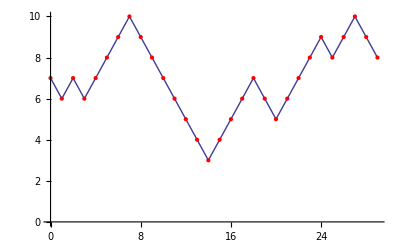

c) Write a function stoprandomwalk[lower, upper, start] that creates a random walk as in part a). However the length is not set, the function  simply stops the walk when the walk (more precisely: the y-coordinate) hits either the number upper or the number lower for the first time. stoprandomwalk[lower, upper, start] should returns the list of coordinates for the walk. Modify this function to create a function stoppointrandomwalk[lower, upper, start]  that only returns the very last coordinate point of the walk, i.e. a single point with coordinates of the form {n, lower} or {n, upper} for some integer n.

d) Write a function lowerupper[lower, upper, start, repeat]  that uses the earlier function stoppointrandomwalk[lower, upper, start]. The function lowerupper[lower, upper, start, repeat] runs stoppointrandomwalk[lower, upper, start] repeat many times and counts and returns how often the walk ends at lower and how often the walk ends at upper.
For example if repeat=10 then it might return {7,3} then this means in the 10 walks generated,  7 walks stopped when they reached the value lower (as y-coordinate) and 3 walks stopped when they reached the value upper (as y-coordinate).

e) Run simulations and collect enough evidence to be able to make a reasonable conjectures about the following:
Given I=[lower,upper] and start what is the probability to hit the value upper (as y-coordinate) and what is the probability to hit the value lower (as y-coordinate)? (Note: assume the range of lower and upper is 10, find the probability for different start value by running thousands of simulations)